```mathematica
Remove["Global`*"]
```

```mathematica
Table[(-1)^n/(2*n+1),{n,0,10}]
```

{1,-1/3,1/5,-1/7,1/9,-1/11,1/13,-1/15,1/17,-1/19,1/21}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]-Pi/4},{m,10,50,10}]
```

{{0.0226808},{0.011898},{0.00806242},{0.00609665},{0.00490149}}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]+(-1)^(m+1)/(4*(m+1))-Pi/4},{m,10,50,10}]
```

{{-0.0000464838},{-6.72973×10^-6},{-2.09523×10^-6},{-9.06162×10^-7},{-4.70935×10^-7}}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]+(-1)^(m+1)*(m+1)/((2*m+2)^2+1)-Pi/4},{m,10,50,10}]
```

{{3.76583×10^-7},{1.51748×10^-8},{2.17462×10^-9},{5.38262×10^-10},{1.80886×10^-10}}

```mathematica
Evaluate@Table[{N[Sum[(-1)^n/(2*n+1),{n,0,m}]]+(-1)^(m+1)*((m+1)^2+1)/((m+1)*((2*m+2)^2+5))-Pi/4},{m,10,50,10}]
```

{{-6.73298×10^-9},{-7.65623×10^-11},{-5.06528×10^-12},{-7.18314×10^-13},{-1.56097×10^-13}}

```mathematica
Remove["Global`*"]
```

```mathematica
g=9.8; v0=5;
x[t_,Theta_] =v0*t*Cos[Theta];
y[t_,h_, Theta_] =h+v0*t*Sin[Theta]-1/2*g*t^2;
```

```mathematica
N[Solve[y[t,h,Theta]==0,t]/.{h->10, Theta->Pi/12}][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{t→1.56671}

```mathematica
FindRoot[{y[t]/.{h->10, Theta->Pi/12}},{t,1}]
```

FindRoot::nlnum: The function value {y[1.]} is not a list of numbers with dimensions {1} at {t} = {1.}.

FindRoot[{y[t]/.{h→10,Theta→π/12}},{t,1}]

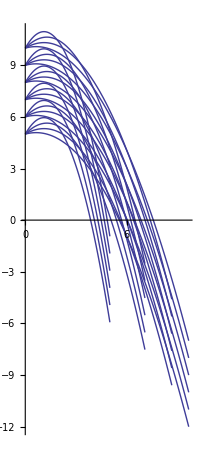

```mathematica
Show[Evaluate@Table[ParametricPlot[{x[t,Theta],y[t,h,Theta]},{t,0,2}],{h,5,10},{Theta, Pi/12,Pi/3,Pi/12}], PlotRange->All]
```

```mathematica
Manipulate[ParametricPlot[{x[t,Theta],y[t,h, Theta]},{t,0,2}],{h,5,10},{Theta, Pi/12,Pi/3,Pi/12}]
```

```mathematica
Table[FindRoot[y[t,h,Theta]/.{h->10},{t,1}],{Theta,Pi/12,Pi/3,Pi/12}]
```

{{t→1.56671},{t→1.70627},{t→1.83419},{t→1.93719}}

```mathematica
Table[FindRoot[y[t,h,Theta]/.{Theta->Pi/12},{t,1}],{h,5,10,1}]
```

{{t→1.1508},{t→1.24647},{t→1.33455},{t→1.41661},{t→1.49373},{t→1.56671}}

```mathematica
Table[NSolve[y[t,h,Pi/12]==0,t][[2]],{h,5,10,1}]
```

{{t→1.1508},{t→1.24647},{t→1.33455},{t→1.41661},{t→1.49373},{t→1.56671}}